```mathematica
data=Import["/home/moritz/Dropbox/BenMoritz/FP2/0427-Z0/data/daten_1.txt","Table"];
```

```mathematica
dataT=Transpose[data];
dataT[[4]]=If[#<150,#,150]&/@dataT[[4]];
names={"run","event","ncharged","pcharged","e_ecal","e_hcal","e_lep","cos_thru","cos_thet"};
```

```mathematica
Cutdata = Select[data, 
#[[3]]==2&&#[[5]]≤50&&#[[4]]≥75&&#[[4]]≤100&&#[[9]]≤1&&#[[7]]≥91.20/2&&#[[7]]≤91.26/2&];
CutdataT=Transpose[Cutdata];
Dimensions[%]
Dimensions[data]
```

{9,3436}

{175883,9}

```mathematica
Dimensions[dataT]
data[[1]]
dataT[[9,1;;10]]
```

{9,94381}

{1602.,1.,2.,63.7694,28.6698,3.41627,45.624,-0.588084,-0.564341}

{-0.564341,0.902914,-0.280375,0.558837,0.432211,-0.217132,0.860958,0.209645,-0.819876,0.0830802}

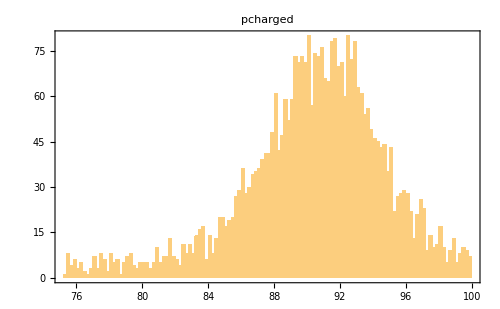

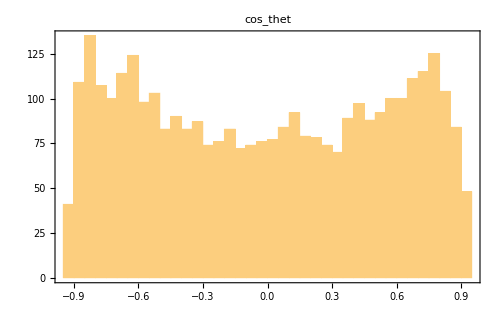

```mathematica
n=4;
Histogram[CutdataT[[n]],100,PlotRange->{All,All},PlotLabel->names[[n]],Frame->True,ImageSize->500]
n=9;
h=Histogram[CutdataT[[n]],50,PlotRange->{All,All},PlotLabel->names[[n]],Frame->True,ImageSize->500]
```

```mathematica
Show[
Histogram3D[Transpose[{dataT[[4]],dataT[[5]]}],{200,200},PlotRange->{{0,150},{0,150},All},ImageSize->700,AxesLabel->{names[[4]],names[[5]]},AxesOrigin->{0,0,0}],ParametricPlot3D[{t,t,0},{t,0,150}]]
```

-Graphics3D-